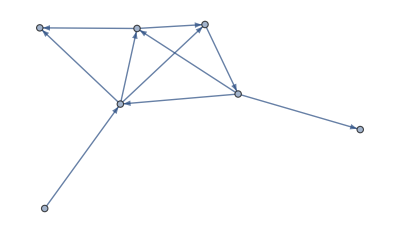

```mathematica
data = Import["/Users/poepping/aoc2021/day12/sample_input_1.txt", "List"];
nolowerdups = Function[ x, DuplicateFreeQ[ Select[x, LowerCaseQ]]];
 data = StringSplit[#,"-"]& /@ data ;
v = StringDelete[ DeleteDuplicates[ Flatten[data] ], {"end", "start"}];
g =Graph[Flatten [ Map[ {#[[1]]-> #[[2]]}&, data]]]
```

```mathematica
tmp =Flatten /@ Tuples[ {FindPath[g, "start", "HN", Infinity, All] ,Rest /@ FindPath[g, "HN", "end", Infinity, All]}
]
```

{{start,kj,HN,end},{start,kj,HN,start,kj,dc,end},{start,kj,dc,HN,end},{start,kj,dc,HN,start,kj,dc,end}}

Function[x,DuplicateFreeQ[Select[x,LowerCaseQ]]]

```mathematica
Select[tmp, nolowerdups]
```

{{start,kj,HN,end},{start,kj,dc,HN,end}}